7: Appendix

#### Figure 1: Example of a simple random network

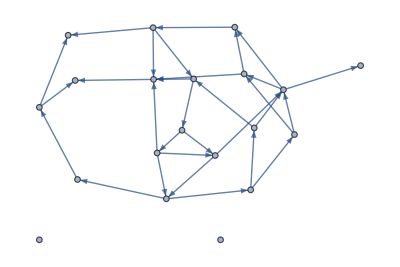

```mathematica
ER[n_,p_]:=Table[If[j==k,0,RandomChoice[{p,1-p}->{1,0}]],{j,1,n},{k,1,n}];
A0=ER[20,0.1];
GraphPlot[A0,DirectedEdges->True]
```

#### Figure 3: Plot showing the gradient-learning model and the scenarios

```mathematica
U[J_]:=m J-c/2 J^2;
D[U[J],J];
Solve[-c J+m==0,J];
DSolve[{D[J[t], t]==α U[J[t]]-β J[t],J[0]==J0},J[t],t];
Plot[{(2 ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) (m α-β))/(-ⅇ^(t β+(ⅈ β (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β))+c ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) α)/.m->5/.c->0.1/.α->0.9/.β->0.9/.J0->0.001,(2 ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) (m α-β))/(-ⅇ^(t β+(ⅈ β (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β))+c ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) α)/.m->5/.c->0.1/.α->0.2/.β->0.2/.J0->0.001,
(2 ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) (m α-β))/(-ⅇ^(t β+(ⅈ β (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β))+c ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) α)/.m->5/.c->0.1/.α->0.9/.β->0.2/.J0->0.001,
(2 ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) (m α-β))/(-ⅇ^(t β+(ⅈ β (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β))+c ⅇ^(m t α+(ⅈ m α (π-ⅈ Log[J0]+ⅈ Log[-c J0 α+2 m α-2 β]))/(m α-β)) α)/.m->5/.c->0.1/.α->0.2/.β->0.9/.J0->0.001},{t,0,100},
FrameLabel->{"t (Time)","J[t] (Number of job applications over time)"},
PlotLabel->Style["Gradient-learning model showing AI impact on job applications",18,Bold,Black],
PlotTheme->"Scientific",
ImageSize->Large,
LabelStyle->Directive[Black,Bold],
PlotLegends->{"Scenario 1","Scenario 2","Scenario 3","Scenario 4"}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

#### Figure 4: TFP over time for a developed and developing country

```mathematica
U[x_]:=α(A x+B x^2);
D[x[t], t]==L D[U[x[t]], x[t]];
Plot[Floor[t],{t,2023,2100},Frame->True]
F[λ_]:=RandomVariate[PoissonDistribution[λ]];
InnovationList0=Table[F[1],{j,1,1000}];
AISchum[t_,InnovationList_]:=AI0 γ^(∑_(k=1)^Floor[t] InnovationList[[k]]);
SolSchum1[Lα_,AI1_,γ1_,x0_,T_,InnovationList_]:=x[t]/.NDSolve[{x'[t]==Lα ((AISchum[t,InnovationList]/.AI0->AI1/.γ->γ1)-x[t]),x[0]==x0},x[t],{t,0,T}][[1]];
Solx1=SolSchum1[0.8,100,0.9,1,100,InnovationList0];
Solx2=SolSchum1[0.2,100,0.9,1,100,InnovationList0];
Plot[{Solx1,Solx2},{t,0,100},
Frame->True,
FrameLabel->{"Time (years from now)","Total Factor Productivity"},
PlotRange->Full,
PlotLabel->Style["Total Factor Productivity over time",20,Bold,Black],
PlotTheme->"Scientific",
PlotLegends->{"Developed country","Developing country"},
LabelStyle->Directive[Black,Bold],
ImageSize->Large]
```

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

#### Figure 5: Development gap in technological progress over time for a developed and developing country

```mathematica
Plot[{Solx1-(AISchum[t,InnovationList0]/.AI0->100/.γ->0.9),
Solx2-(AISchum[t,InnovationList0]/.AI0->100/.γ->0.9)},{t,0,100},
Frame->True,
FrameLabel->{"Time (years from now)","Development-gap"},
PlotRange->Full,
PlotLabel->Style["Development gap over time",20,Bold,Black],
PlotTheme->"Scientific",
PlotLegends->{"Developed country","Developing country"},
LabelStyle->Directive[Black,Bold],
ImageSize->Large]
```